```mathematica
(* Calibration *)
```

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

```mathematica
<<ErrorBarPlots`
```

```mathematica
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx,bm,ctex}"},"Magnification"->1.5];
MyTeX[x_]:=HideText[MaTeX[x]];
HideText["* Some Basic setup *"]
```

* Some Basic setup *

```mathematica
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\xelatex.exe"];*)
(*ConfigureMaTeX["pdfLaTeX"->"C:\\texlive\\2016\\bin\\win32\\pdflatex.exe"];*)
HideText["* Engine unchanged, possibly pdfLaTeX *"]
```

* Engine unchanged, possibly pdfLaTeX *

```mathematica
omarker=Graphics[{Thickness[.2],Circle[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
csDataRAW=Import["data.xlsx"]⟦3⟧⟦All,{1,2}⟧;
coDataRAW=Import["data.xlsx"]⟦3⟧⟦All,{4,5}⟧;
```

```mathematica
sigma=6;
FindPeaks[#,sigma]&/@{csDataRAW,coDataRAW}⟦All,2;;,2⟧//N;
%//Column
cscoPeaks=AssociationThread[{"cs","co"},Select[20<#⟦1⟧<350&]/@%%];
cscoPeaks//Dataset
```

{{13.,1458.},{43.,1011.},{151.,612.},{266.,26.},{304.,16.},{380.5,2.},{406.5,2.},{411.,2.},{442.,2.},{484.5,1.},{512.,1.}}
{{14.,1663.},{204.,322.},{267.,215.},{307.,145.},{365.,4.},{367.,3.},{369.,4.},{429.,3.},{455.,2.},{477.,3.},{512.,4.}}

Dataset[<>]

```mathematica
csPeaks=cscoPeaks["cs"]⟦;;2⟧
coPeaks=cscoPeaks["co"]⟦2;;⟧
```

{{43.,1011.},{151.,612.}}

{{267.,215.},{307.,145.}}

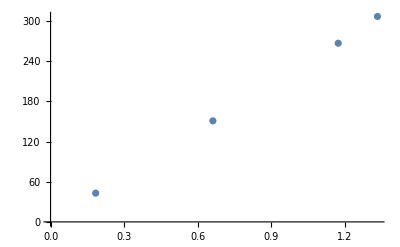

FittedModel[0.240468+228.83 x]

{2.4×10^-1,2.29×10^2}

{2.,2.}

{8.01839,0.00885141}

```mathematica
calData={{.184,.662,1.173,1.333},csPeaks⟦All,1⟧~Join~coPeaks⟦All,1⟧}ᵀ;
ListPlot[%,PlotRange->{{0,All},{0,All}}]
calFunction=LinearModelFit[calData,x,x]
calFunction["BestFitParameters"]//NumberForm[#,3]&//ScientificForm
calFunction["ParameterErrors"]//NumberForm[#,1]&//ScientificForm
calFunction["ParameterErrors"]/calFunction["BestFitParameters"]
```

```mathematica
calFunction["RSquared"]
```

0.999843

```mathematica
eFunction[n_]=x/.(Solve[n==calFunction//Normal,x]//Flatten)
```

-0.00437006 (0.240468-n)

```mathematica
calFunction["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.240468 | 1.92817 | 0.124713 | 0.912155
x | 228.83 | 2.02547 | 112.976 | 0.0000783383

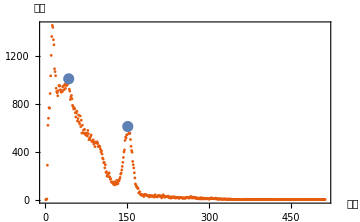

csPlot.pdf

```mathematica
csPlot=Show[ListPlot[csDataRAW,
PlotTheme->"Scientific",
PlotRange->{0,All},
PlotRangePadding->{{0,0},{0,Automatic}},
ImagePadding->{{50,40},{25,30}},
ImageSize->Medium,
GridLines->None],
ListPlot[csPeaks,
PlotMarkers->{omarker,.04}],
Epilog->(Inset[Evaluate@Style[#1,FontFamily->"黑体",FontSize->10.5],#2]&)@@@{{"道址",Scaled[{1.075,0}]},{"计数",Scaled[{0,1.08}]}},
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@csPlot
```

```mathematica
SystemOpen["csPlot.pdf"]
```

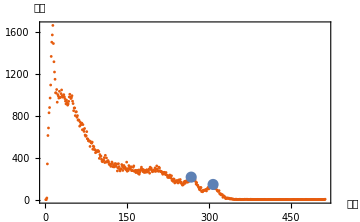

coPlot.pdf

```mathematica
coPlot=Show[ListPlot[coDataRAW,
PlotTheme->"Scientific",
PlotRange->{0,All},
PlotRangePadding->{{0,0},{0,Automatic}},
ImagePadding->{{50,40},{25,30}},
ImageSize->Medium,
GridLines->None],
ListPlot[coPeaks,
PlotMarkers->{omarker,.04}],
Epilog->(Inset[Evaluate@Style[#1,FontFamily->"黑体",FontSize->10.5],#2]&)@@@{{"道址",Scaled[{1.075,0}]},{"计数",Scaled[{0,1.08}]}},
PlotRangeClipping->False]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@coPlot
```